```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
controlColor=Black;
```

```mathematica
(****************************)
```

```mathematica
dateMouseListControl={{"113021","Mouse22428"},{"120221","Mouse22525"},{"121621","Mouse22525"},{"010622","Mouse22598"},{"011122","Mouse22598"},{"121121","Mouse22599"},{"121721","Mouse22599"},{"012122","Mouse22550"},{"011622","Mouse22550"},{"012322","Mouse22549"},{"012822","Mouse22549"},{"032923","Mouse23149"},{"033123","Mouse23149"}};
```

```mathematica
(***V1 axons, eOPN3***)
```

```mathematica
dateMouseListV1axons={{"120921","Mouse22485"},{"121821","Mouse22485"},{"011222","Mouse22501"},{"011822","Mouse22504"},{"012722","Mouse22504"},{"012322","Mouse22575"}};
```

```mathematica
(***LPaxons, eOPN3***)
```

```mathematica
dateMouseListLPaxons={{"020922","Mouse22413"},{"021422","Mouse22413"},{"020122","Mouse22514"},{"012822","Mouse22514"},{"021122","Mouse22519"},{"021322","Mouse22519"},{"021122","Mouse22535"},{"021522","Mouse22535"},{"031522","Mouse22521"},{"031922","Mouse22521"}};
```

```mathematica
(***LM axons, eOPN3***)
```

```mathematica
dateMouseListLMaxons={{"022022","Mouse22563"},{"022222","Mouse22563"},{"031722","Mouse22539"},{"031722","Mouse22570"},{"032022","Mouse22539"},{"032022","Mouse22570"}};
```

```mathematica
(*****************************)
```

```mathematica
pairedROIsListControl=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_pairedROIsLoc.txt"],"List"],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pairedROIsListV1axons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_pairedROIsLoc.txt"],"List"],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pairedROIsListLPaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_pairedROIsLoc.txt"],"List"],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pairedROIsListLMaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_pairedROIsLoc.txt"],"List"],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
(*******Control*******)
```

```mathematica
periOnsetDFFzTimeSeriesControlDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/","Session1","/LocomotionData/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_","Session1","_","PeriOnsetZDFF_PreAndPostBaseline_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListControl[[n]]}],{n,1,Length[dateMouseListControl]}];
```

```mathematica
periOnsetDFFzTimeSeriesControlLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/","Session2","/LocomotionData/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_","Session2","_","PeriOnsetZDFF_PreAndPostBaseline_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListControl[[n]]}],{n,1,Length[dateMouseListControl]}];
```

```mathematica
catenatedLocModOnsetControlDark=Flatten[periOnsetDFFzTimeSeriesControlDark,1];
```

```mathematica
catenatedLocModOnsetControlLED=Flatten[periOnsetDFFzTimeSeriesControlLED,1];
```

```mathematica
meanCatenatedLocModOnsetControlDark=Mean[catenatedLocModOnsetControlDark];
```

```mathematica
semCatenatedLocModOnsetControlDark=(#/Sqrt@Length[catenatedLocModOnsetControlDark])&/@StandardDeviation[catenatedLocModOnsetControlDark];
```

```mathematica
meanCatenatedLocModOffsetControlDark=Mean[catenatedLocModOffsetControlDark];
```

```mathematica
semCatenatedLocModOffsetControlDark=(#/Sqrt@Length[catenatedLocModOffsetControlDark])&/@StandardDeviation[catenatedLocModOffsetControlDark];
```

```mathematica
meanCatenatedLocModOnsetControlLED=Mean[catenatedLocModOnsetControlLED];
```

```mathematica
semCatenatedLocModOnsetControlLED=(#/Sqrt@Length[catenatedLocModOnsetControlLED])&/@StandardDeviation[catenatedLocModOnsetControlLED];
```

```mathematica
meanCatenatedLocModOffsetControlLED=Mean[catenatedLocModOffsetControlLED];
```

```mathematica
semCatenatedLocModOffsetControlLED=(#/Sqrt@Length[catenatedLocModOffsetControlLED])&/@StandardDeviation[catenatedLocModOffsetControlLED];
```

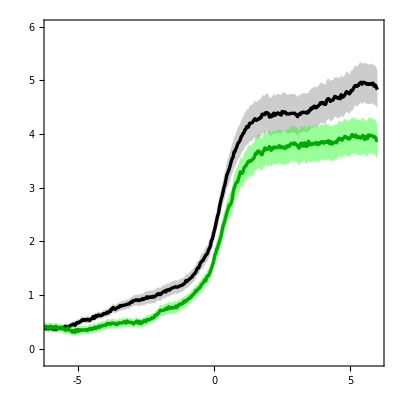

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedLocModOnsetControlDark,Part[#,2]&/@meanCatenatedLocModOnsetControlDark+(Part[#,2]&/@semCatenatedLocModOnsetControlDark),Part[#,2]&/@meanCatenatedLocModOnsetControlDark-(Part[#,2]&/@semCatenatedLocModOnsetControlDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-15,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],ListLinePlot[{Part[#,2]&/@meanCatenatedLocModOnsetControlLED,Part[#,2]&/@meanCatenatedLocModOnsetControlLED+(Part[#,2]&/@semCatenatedLocModOnsetControlLED),Part[#,2]&/@meanCatenatedLocModOnsetControlLED-(Part[#,2]&/@semCatenatedLocModOnsetControlLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-15,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],AspectRatio->1]
```

```mathematica
(*******V1 eOPN3*******)
```

```mathematica
periOnsetDFFzTimeSeriesV1axonsDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/","Session1","/LocomotionData/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_","Session1","_","PeriOnsetZDFF_PreAndPostBaseline_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
periOnsetDFFzTimeSeriesV1axonsLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/","Session2","/LocomotionData/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_","Session2","_","PeriOnsetZDFF_PreAndPostBaseline_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
catenatedLocModOnsetV1axonsDark=Flatten[periOnsetDFFzTimeSeriesV1axonsDark,1];
```

```mathematica
catenatedLocModOnsetV1axonsLED=Flatten[periOnsetDFFzTimeSeriesV1axonsLED,1];
```

```mathematica
meanCatenatedLocModOnsetV1axonsDark=Mean[catenatedLocModOnsetV1axonsDark];
```

```mathematica
semCatenatedLocModOnsetV1axonsDark=(#/Sqrt@Length[catenatedLocModOnsetV1axonsDark])&/@StandardDeviation[catenatedLocModOnsetV1axonsDark];
```

```mathematica
meanCatenatedLocModOffsetV1axonsDark=Mean[catenatedLocModOffsetV1axonsDark];
```

```mathematica
semCatenatedLocModOffsetV1axonsDark=(#/Sqrt@Length[catenatedLocModOffsetV1axonsDark])&/@StandardDeviation[catenatedLocModOffsetV1axonsDark];
```

```mathematica
meanCatenatedLocModOnsetV1axonsLED=Mean[catenatedLocModOnsetV1axonsLED];
```

```mathematica
semCatenatedLocModOnsetV1axonsLED=(#/Sqrt@Length[catenatedLocModOnsetV1axonsLED])&/@StandardDeviation[catenatedLocModOnsetV1axonsLED];
```

```mathematica
meanCatenatedLocModOffsetV1axonsLED=Mean[catenatedLocModOffsetV1axonsLED];
```

```mathematica
semCatenatedLocModOffsetV1axonsLED=(#/Sqrt@Length[catenatedLocModOffsetV1axonsLED])&/@StandardDeviation[catenatedLocModOffsetV1axonsLED];
```

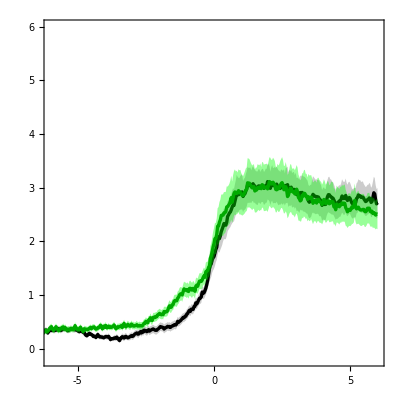

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedLocModOnsetV1axonsDark,Part[#,2]&/@meanCatenatedLocModOnsetV1axonsDark+(Part[#,2]&/@semCatenatedLocModOnsetV1axonsDark),Part[#,2]&/@meanCatenatedLocModOnsetV1axonsDark-(Part[#,2]&/@semCatenatedLocModOnsetV1axonsDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-15,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],ListLinePlot[{Part[#,2]&/@meanCatenatedLocModOnsetV1axonsLED,Part[#,2]&/@meanCatenatedLocModOnsetV1axonsLED+(Part[#,2]&/@semCatenatedLocModOnsetV1axonsLED),Part[#,2]&/@meanCatenatedLocModOnsetV1axonsLED-(Part[#,2]&/@semCatenatedLocModOnsetV1axonsLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-15,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],AspectRatio->1]
```

```mathematica
(*******LP eOPN3*******)
```

```mathematica
periOnsetDFFzTimeSeriesLPaxonsDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/","Session1","/LocomotionData/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_","Session1","_","PeriOnsetZDFF_PreAndPostBaseline_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
periOnsetDFFzTimeSeriesLPaxonsLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/","Session2","/LocomotionData/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_","Session2","_","PeriOnsetZDFF_PreAndPostBaseline_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
catenatedLocModOnsetLPaxonsDark=Flatten[periOnsetDFFzTimeSeriesLPaxonsDark,1];
```

```mathematica
catenatedLocModOnsetLPaxonsLED=Flatten[periOnsetDFFzTimeSeriesLPaxonsLED,1];
```

```mathematica
meanCatenatedLocModOnsetLPaxonsDark=Mean[catenatedLocModOnsetLPaxonsDark];
```

```mathematica
semCatenatedLocModOnsetLPaxonsDark=(#/Sqrt@Length[catenatedLocModOnsetLPaxonsDark])&/@StandardDeviation[catenatedLocModOnsetLPaxonsDark];
```

```mathematica
meanCatenatedLocModOffsetLPaxonsDark=Mean[catenatedLocModOffsetLPaxonsDark];
```

```mathematica
semCatenatedLocModOffsetLPaxonsDark=(#/Sqrt@Length[catenatedLocModOffsetLPaxonsDark])&/@StandardDeviation[catenatedLocModOffsetLPaxonsDark];
```

```mathematica
meanCatenatedLocModOnsetLPaxonsLED=Mean[catenatedLocModOnsetLPaxonsLED];
```

```mathematica
semCatenatedLocModOnsetLPaxonsLED=(#/Sqrt@Length[catenatedLocModOnsetLPaxonsLED])&/@StandardDeviation[catenatedLocModOnsetLPaxonsLED];
```

```mathematica
meanCatenatedLocModOffsetLPaxonsLED=Mean[catenatedLocModOffsetLPaxonsLED];
```

```mathematica
semCatenatedLocModOffsetLPaxonsLED=(#/Sqrt@Length[catenatedLocModOffsetLPaxonsLED])&/@StandardDeviation[catenatedLocModOffsetLPaxonsLED];
```

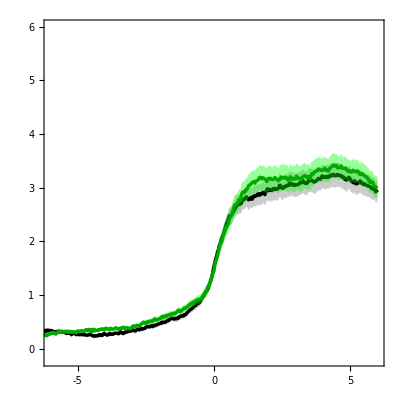

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedLocModOnsetLPaxonsDark,Part[#,2]&/@meanCatenatedLocModOnsetLPaxonsDark+(Part[#,2]&/@semCatenatedLocModOnsetLPaxonsDark),Part[#,2]&/@meanCatenatedLocModOnsetLPaxonsDark-(Part[#,2]&/@semCatenatedLocModOnsetLPaxonsDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-15,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],ListLinePlot[{Part[#,2]&/@meanCatenatedLocModOnsetLPaxonsLED,Part[#,2]&/@meanCatenatedLocModOnsetLPaxonsLED+(Part[#,2]&/@semCatenatedLocModOnsetLPaxonsLED),Part[#,2]&/@meanCatenatedLocModOnsetLPaxonsLED-(Part[#,2]&/@semCatenatedLocModOnsetLPaxonsLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-15,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],AspectRatio->1]
```

```mathematica
(*******LM eOPN3*******)
```

```mathematica
periOnsetDFFzTimeSeriesLMaxonsDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/","Session1","/LocomotionData/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_","Session1","_","PeriOnsetZDFF_PreAndPostBaseline_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
periOnsetDFFzTimeSeriesLMaxonsLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/","Session2","/LocomotionData/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_","Session2","_","PeriOnsetZDFF_PreAndPostBaseline_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
catenatedLocModOnsetLMaxonsDark=Flatten[periOnsetDFFzTimeSeriesLMaxonsDark,1];
```

```mathematica
catenatedLocModOnsetLMaxonsLED=Flatten[periOnsetDFFzTimeSeriesLMaxonsLED,1];
```

```mathematica
meanCatenatedLocModOnsetLMaxonsDark=Mean[catenatedLocModOnsetLMaxonsDark];
```

```mathematica
semCatenatedLocModOnsetLMaxonsDark=(#/Sqrt@Length[catenatedLocModOnsetLMaxonsDark])&/@StandardDeviation[catenatedLocModOnsetLMaxonsDark];
```

```mathematica
meanCatenatedLocModOffsetLMaxonsDark=Mean[catenatedLocModOffsetLMaxonsDark];
```

```mathematica
semCatenatedLocModOffsetLMaxonsDark=(#/Sqrt@Length[catenatedLocModOffsetLMaxonsDark])&/@StandardDeviation[catenatedLocModOffsetLMaxonsDark];
```

```mathematica
meanCatenatedLocModOnsetLMaxonsLED=Mean[catenatedLocModOnsetLMaxonsLED];
```

```mathematica
semCatenatedLocModOnsetLMaxonsLED=(#/Sqrt@Length[catenatedLocModOnsetLMaxonsLED])&/@StandardDeviation[catenatedLocModOnsetLMaxonsLED];
```

```mathematica
meanCatenatedLocModOffsetLMaxonsLED=Mean[catenatedLocModOffsetLMaxonsLED];
```

```mathematica
semCatenatedLocModOffsetLMaxonsLED=(#/Sqrt@Length[catenatedLocModOffsetLMaxonsLED])&/@StandardDeviation[catenatedLocModOffsetLMaxonsLED];
```

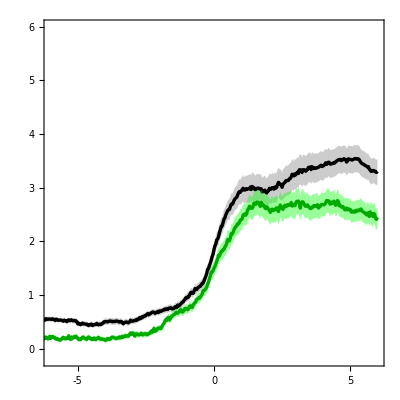

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedLocModOnsetLMaxonsDark,Part[#,2]&/@meanCatenatedLocModOnsetLMaxonsDark+(Part[#,2]&/@semCatenatedLocModOnsetLMaxonsDark),Part[#,2]&/@meanCatenatedLocModOnsetLMaxonsDark-(Part[#,2]&/@semCatenatedLocModOnsetLMaxonsDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-15,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],ListLinePlot[{Part[#,2]&/@meanCatenatedLocModOnsetLMaxonsLED,Part[#,2]&/@meanCatenatedLocModOnsetLMaxonsLED+(Part[#,2]&/@semCatenatedLocModOnsetLMaxonsLED),Part[#,2]&/@meanCatenatedLocModOnsetLMaxonsLED-(Part[#,2]&/@semCatenatedLocModOnsetLMaxonsLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-15,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],AspectRatio->1]
```